### The exp[bx] Maclauren expansion for small x

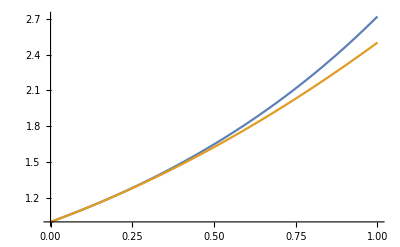

```mathematica
Remove[b]
fx=Exp[b*x];
gx=1+b*x+(1/2)b^2*x^2 (*+ (1/3!)*b^3*x^3 + (1/4!)*b^4*x^4 *);
b=1;
Plot[{fx,gx},{x,0,1}]
```

{{x→0},{x→(2 (-1+ab))/ab^2}}

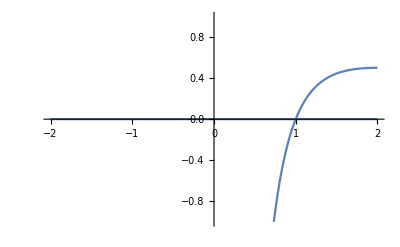

```mathematica
FP=Solve[x(1-ab)+(1/2*ab^2)*x^2==0,x]
Plot[x/.FP,{ab,-2,2},PlotRange->{-1,1}]
```